# Exoplanets

Doppler spectroscopy method description and a brief comparative analysis between known exoplanets.

Domenico Romano, Jun. 29,  2018

As the word says, an exoplanet is a planet outside our Solar System. At the moment there are 3786 confirmed planets in 2834 systems, more than 600 systems possess more than one planet. When possible to infer their physical characteristics, an exoplanet could be classified into these three main classes:

```mathematica
ExoplanetData["Classes"]
```

```mathematica
{EntityClass["Exoplanet","SuperEarth"],EntityClass["Exoplanet","HotNeptune"],EntityClass["Exoplanet","HotJupiter"]}
```

A super-Earth planet defines a planet which possess a mass up to 15 to 17 Earth masses. Despite the name, a super-Earth planet could possess characteristics which are far from supporting life as we known. The first super-Earths discovered were

```mathematica
Entity["Star","PSRB1257Plus12"][EntityProperty["Star","Satellites"]]
```

{PSR B1257+12 b,PSR B1257+12 c,PSR B1257+12 d}

Around a Pulsar star at:

```mathematica
StarData[Entity["Star","PSRB1257Plus12"],"DistanceFromSun"]
```

0.599589 kpc

from Sun.

Hot-Neptunes  have a mass comparable to Uranus/Neptune, orbiting very close to their host star (orbit radius < 1 a.u.). The first hot Neptune exoplanet discovered was Gliese 436 b in 2007.

Hot-Jupiters are gas giants planets like Jupiter with a very short orbital period (p < 10 days). Thus, their vicinity to the mother star results in high surface temperatures, hence the prefix “hot”. The first hot-Jupiter discovered was 51 Pegasi b, in 1995, via radial-velocity method. Its mass compared to Earth mass is:

```mathematica
ExoplanetData[Entity["Exoplanet","51Pegasib"],"Mass"]/Entity["Planet","Earth"][EntityProperty["Planet","Mass"]]
```

150.01

## Exoplanet distribution around the Sun

The actual three-dimensional distribution, with respect to the Sun, of the known star systems is:

```mathematica
Iconize[{Axes->{True,True,True},AxesLabel->{x-pc,y-pc, z-pc},ImageSize->Large},"opt1"]
```

```mathematica
Graphics3D[{Point[QuantityMagnitude[DeleteMissing[ExoplanetData[All,"HelioCoordinates"]]]/3.26],
PointSize[Tiny]},]
(* 3D distribution of discovered exoplanets based on heliocentric coordinates *)
```

-Graphics3D-

Negative distances represent a convection of the adopted rectangular galactic coordinates. In this particular system negative y are towards the  Galaxy center, while positive x and z are towards astronomical East and the North Galactic Pole .

This 3D distribution reflects our current level of knowledge and is far to be complete. The “cone” shape, composed by thousands of stellar systems, represent the sky portion surveyed by the last generation instruments. Assuming exoplanet are isotropically distributed around the Sun, the number of new stellar systems to be discovered in the near future will dramatically increase.

It is important to specify that the Sun is in a privileged region of our Galaxy, being sufficiently far from the Galaxy center to not be interested by violent phenomena and not too far to be poor of heavy elements necessary for life.

## Doppler spectroscopy or Radial-Velocity method

#### Barycenter position depending on star-planet characteristics

Around 30% of exoplanets were discovered by using the radial-velocity method.

Two gravitationally bounded bodies move around a common barycenter, which corresponds to one of the foci of their orbits. Considering a star-planet system, indicating with distance the distance between the two bodies, with massStar and massPlanet respectively the star mass and the planet mass in Earth masses, the following function gives the position of the barycenter with respect to the star center:

```mathematica
Manipulate[
Plot[(distance *massPlanet)/(massStar+massPlanet)*150000000,{massStar,10^5,10^7},PlotRange->Automatic],
{distance,1,20},{massPlanet,1,400},SaveDefinitions->True]
(* Barycenter positions [in km from star center] in function of the host star mass expressed in Earth masses *)
```

If the barycenter lies within the star radius the star appear to “wobble” around it, instead of following a proper orbit. The greater is the distance between the barycenter and the star center the greater is the Doppler effect. This could be detected by an observer co-planar with the star-planet orbital plane, making it possible to quantify the star radial velocity change over a time interval (defined as the star velocity variation along the observer line of sight).

Measuring radial velocity change

The star light is observed over a period of time, looking for periodic changes in the frequency of the star spectral lines, making possible to infer a typical sine curve of the star radial velocity:

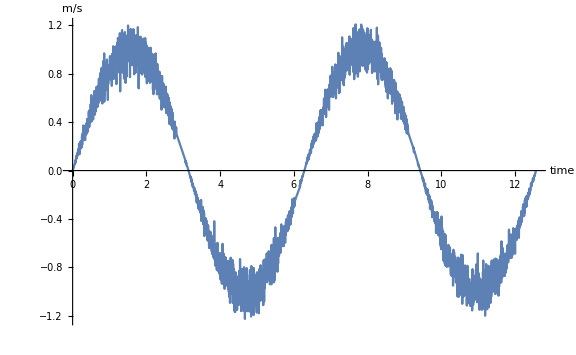

```mathematica
Plot[Sin[x]*RandomReal[NormalDistribution[1,.1]],{x,0,4π},AxesLabel->{"time","m/s"},ImageSize->Large]
```

The plot above represent a radial velocity change of about 1 m/s.

Starting from this quantity it is possible to derive additional informations on the orbiting planet.

Rewriting the third Kepler law it is possible to write the planet distance from the star, distPlanet:

```mathematica
distPlanet=((Quantity[, "GravitationalConstant"] *starMass *periodStar^2)/(4π))^(1/3)
```

(periodStar^2 starMass (1/(4 π) G))^(1/3)

Having the distance of the planet, the orbital velocity, velPlanet, can be derived as following:

```mathematica
velPlanet=Sqrt[starMass*velStar/distPlanet]
```

√((radVel starMass Csc[inclSystem])/((periodStar^2 starMass (1/(4 π) G))^(1/3)))

Here the star velocity, velStar, is computed from the observed star radial velocity, radVel, making assumption on the inclination of the star system orbital plane (inclSystem) with respect to the line of sight:

```mathematica
velStar=(radVel / Sin[inclSystem])
```

radVel Csc[inclSystem]

The planet mass can be derived from the planet velocity, velPlanet, putting all together:

```mathematica
massPlanet=(radVel starMass Csc[inclSystem])/(√((radVel starMass Csc[inclSystem])/((periodStar^2 starMass (Quantity[1/(4 π), "GravitationalConstant"]))^(1/3))))
```

## Exoplanets main characteristics

Following is presented the distribution of exoplanet masses and their distances from Sun, according to their different classification. In red are  those planets which do not have a definitive classification.

```mathematica
planetData=Reverse@SortBy[GroupBy[Select[ExoplanetData[EntityClass["Exoplanet",All],{"DistanceFromSun","Mass" ,"Classes"}]!MatchQ[#[[3]],Missing["NotAvailable"]]&],Last->Most],Length[#]&];
```

```mathematica
Iconize[{Frame->True,FrameLabel->{"Distance (ly)","mass (Earth masses)"},PlotStyle->PointSize[Medium],PlotLegends->Placed[PointLegend[DeleteDuplicates[Flatten[Keys[planData]]],LegendLabel->"Planet type",LegendFunction->"Panel",LegendLayout->Automatic],Right],TargetUnits->{"ly","EarthMass"},ImageSize->Large,LabelingFunction->Callout},"opt2"]
```

```mathematica
ListLogLogPlot[planetData,]
```

-Graphics-

In the plot above the exoplanet realm extremes are marked with labels.

#### Comparative study of exoplanets Semi Major axis distributions

Looking deeper at the CDF of the Log Semi-Major Axis, for each classes of exoplanets:

```mathematica
terraSemiMajor=Log[QuantityMagnitude[UnitConvert[
DeleteMissing[ExoplanetData[EntityClass["Exoplanet","SuperEarth"],"SemimajorAxis"]],
"AstronomicalUnit"]]];
hotJupiterSemiMajor=Log[QuantityMagnitude[UnitConvert[
DeleteMissing[ExoplanetData[LinguisticAssistant,"SemimajorAxis"]],
"AstronomicalUnit"]]];
hotNeptuneSemiMajor=Log[QuantityMagnitude[UnitConvert[
DeleteMissing[ExoplanetData[LinguisticAssistant,"SemimajorAxis"]],
"AstronomicalUnit"]]];
```

```mathematica
Iconize[{AxesLabel->{"Log(au)"},PlotLabel->Style["Semi Major Axis CDF for exoplanets divided by classes"],
ChartStyle->65,ChartLayout->"Stacked",ChartLegends->{"hot-Jupiter","hot-Neptune","super-Earth"},ImageSize->Large},"opt3"]
```

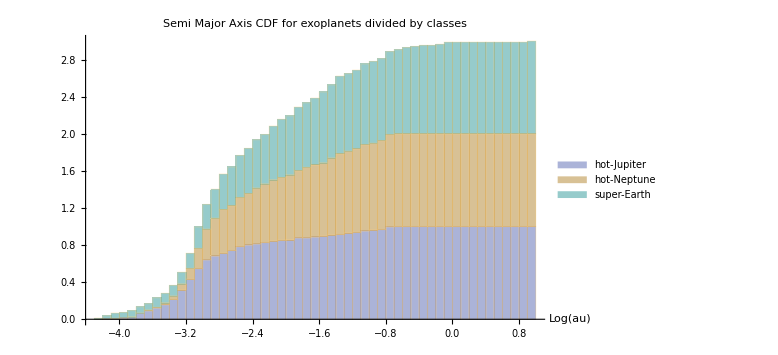

```mathematica
Histogram[{hotJupiterSemiMajor,hotNeptuneSemiMajor,terraSemiMajor},{0.1},"CDF",]
```

It is possible to note most of the detected hot-Jupiters are at a closer distance from their host star compared to hot-Neptunes or super-Earths, the latter show a broader distribution with a tail at longer distances.

#### Comparative study of exoplanets Mass Distribution

```mathematica
terraMass=Log[QuantityMagnitude[UnitConvert[
DeleteMissing[ExoplanetData[EntityClass["Exoplanet","SuperEarth"],"Mass"]],
"EarthMass"]]];
hotJupiterMass=Log[QuantityMagnitude[UnitConvert[
DeleteMissing[ExoplanetData[LinguisticAssistant,"Mass"]],
"EarthMass"]]];
hotNeptuneMass=Log[QuantityMagnitude[UnitConvert[
DeleteMissing[ExoplanetData[LinguisticAssistant,"Mass"]],
"EarthMass"]]];
```

```mathematica
Iconize[{AxesLabel->{"Log(Earth Masses)"},PlotLabel->Style["Mass Distribution CDF for exoplanets divided by classes"],
ChartStyle->63,ChartLayout->"Stacked",ChartLegends->{"hot-Jupiter","hot-Neptune","super-Earth"},ImageSize->Large},"opt4"]
```

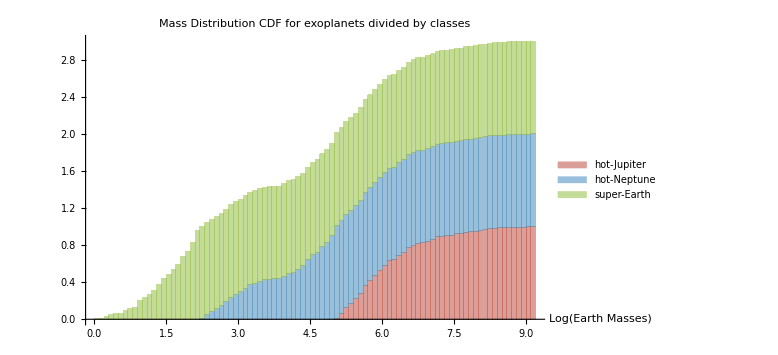

```mathematica
Histogram[{hotJupiterMass,hotNeptuneMass,terraMass},{0.1},"CDF",]
```

In the plot is clearly shown how differently the exoplanet are distributed according to their class.

## Further explorations

- Expand the exoplanet database in order to create a solid statistics on them, helping in the creation of more accurate model

- Develop Virtual Reality and Augmented Reality application in order to visualise exoplanet data in a more human readable way

### Author contact information

domenico.romano@student.unsw.edu.au